```mathematica
f[x_]:= 3Sin[3x]+x^2
```

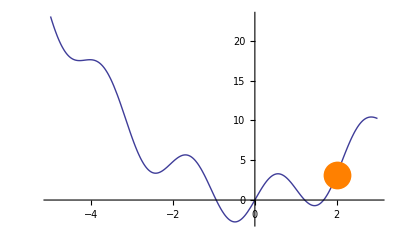

```mathematica
Show[Plot[f[x],{x,-5,3}],Graphics[{Orange,PointSize[.05],Point[{2,f[2]}]}]]
```

```mathematica
k = 2;
```

```mathematica
Slider[Dynamic[k],{-5,3}]
```

```mathematica
Show[{Plot[f[x],{x,-5,3}],Graphics[{Orange,PointSize[.05],Dynamic[Point[{k,f[k]}]]},ImageSize->Large]}]
```

-Graphics-